```mathematica
a=5;
r[t_]={Cos[t]Sin[5t],Sin[t]Sin[5t],Cos[5t]};
curve=ParametricPlot3D[r[t],{t,0,2Pi}]
r'[t]
```

-Graphics3D-

{5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t],5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t],-5 Sin[5 t]}

```mathematica
T[t_]=r'[t]/Sqrt[r'[t].r'[t]]
```

{(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)),(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)),-(5 Sin[5 t])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))}

```mathematica
circle[b_,θ_,t_]=Piecewise[Table[{b{Cos[θ],Sin[θ],-T[t].{Cos[θ],Sin[θ],0}/T[t].{0,0,1}},t≠ i Pi/a},{i,0,2 a}],Table[{b{Cos[θ],-T[t].{Cos[θ],0,Sin[θ]}/T[t].{0,1,0},Sin[θ]},t== i Pi/a},{i,0,2 a}]]
```

Piecewise[{{{b Cos[θ],b Sin[θ],-1/5 b Csc[5 t] √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))-((5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t]) Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))}, t≠0||t≠π/5||t≠(2 π)/5||t≠(3 π)/5||t≠(4 π)/5||t≠π||t≠(6 π)/5||t≠(7 π)/5||t≠(8 π)/5||t≠(9 π)/5||t≠2 π}, {{{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==0},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(2 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(3 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(4 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(6 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(7 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(8 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(9 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==2 π}}, True}}]

```mathematica
Piecewise[{{{b Cos[θ],b Sin[θ],-1/5 b Csc[5 t] √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))-((5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t]) Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))}, t≠0||t≠π/5||t≠(2 π)/5||t≠(3 π)/5||t≠(4 π)/5||t≠π||t≠(6 π)/5||t≠(7 π)/5||t≠(8 π)/5||t≠(9 π)/5||t≠2 π}, {{{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==0},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(2 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(3 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(4 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(6 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(7 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(8 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(9 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==2 π}}, True}}]
```

Piecewise[{{{b Cos[θ],b Sin[θ],-1/5 b Csc[5 t] √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))-((5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t]) Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))}, t≠0||t≠π/5||t≠(2 π)/5||t≠(3 π)/5||t≠(4 π)/5||t≠π||t≠(6 π)/5||t≠(7 π)/5||t≠(8 π)/5||t≠(9 π)/5||t≠2 π}, {{{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==0},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(2 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(3 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(4 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(6 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(7 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(8 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(9 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==2 π}}, True}}]

```mathematica
circle1[b_,θ_,t_]=Piecewise[Table[{b{Cos[θ],-T[t].{Cos[θ],Sin[θ],0}/T[t].{0,0,1},Sin[θ]},t≠ i Pi/a},{i,0,2 a}],Table[{b{Cos[θ],-T[t].{Cos[θ],0,Sin[θ]}/T[t].{0,1,0},Sin[θ]},t== i Pi/a},{i,0,2 a}]]
```

Piecewise[{{{b Cos[θ],-1/5 b Csc[5 t] √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))-((5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t]) Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]}, t≠0||t≠π/5||t≠(2 π)/5||t≠(3 π)/5||t≠(4 π)/5||t≠π||t≠(6 π)/5||t≠(7 π)/5||t≠(8 π)/5||t≠(9 π)/5||t≠2 π}, {{{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==0},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(2 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(3 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(4 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(6 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(7 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(8 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(9 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==2 π}}, True}}]

```mathematica
ParametricPlot3D[circle1[.01,θ,t]+r[t],{θ,0,2 Pi},{t,0+.02,Pi/5-.02}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[circle[.01,θ,t]+r[t],{θ,0,2 Pi},{t,0+.02,Pi/5-.02}]
```

-Graphics3D-

```mathematica
object = Show[Table[ParametricPlot3D[circle[.01,θ,t]+r[t],{θ,0,2 Pi},{t,i Pi/5+.02,(i+1)Pi/5-.02}],{i,0,9}],PlotRange-> All]
```

-Graphics3D-

```mathematica
object1 = Show[Table[ParametricPlot3D[circle1[.01,θ,t]+r[t],{θ,0,2 Pi},{t,i Pi/5+.02,(i+1)Pi/5-.02}],{i,0,9}],PlotRange-> All]
```

-Graphics3D-

```mathematica
circle2[b_,θ_,t_]=Piecewise[Table[{b{-T[t].{Cos[θ],Sin[θ],0}/T[t].{0,0,6},Cos[θ],Sin[θ]},t≠ i Pi/a},{i,0,2 a}],Table[{b{Cos[θ],-T[t].{Cos[θ],0,Sin[θ]}/T[t].{0,1,0},Sin[θ]},t== i Pi/a},{i,0,2 a}]]
```

Piecewise[{{{-1/30 b Csc[5 t] √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))-((5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t]) Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Cos[θ],b Sin[θ]}, t≠0||t≠π/5||t≠(2 π)/5||t≠(3 π)/5||t≠(4 π)/5||t≠π||t≠(6 π)/5||t≠(7 π)/5||t≠(8 π)/5||t≠(9 π)/5||t≠2 π}, {{{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==0},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(2 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(3 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(4 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(6 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(7 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(8 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(9 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==2 π}}, True}}]

```mathematica
ParametricPlot3D[circle2[.01,θ,t]+r[t],{θ,0,2 Pi},{t,0+.02,Pi/5-.02}]
```

-Graphics3D-

```mathematica
object2 = Show[Table[ParametricPlot3D[circle2[.01,θ,t]+r[t],{θ,0,2 Pi},{t,i Pi/5+.02,(i+1)Pi/5-.02}],{i,0,9}],PlotRange-> All]
```

-Graphics3D-

```mathematica
circle3[b_,θ_,t_]=Piecewise[Table[{b{-T[t].{Cos[θ],Sin[θ],0}/T[t].{0,0,30},Cos[θ],Sin[θ]},t≠ i Pi/a},{i,0,2 a}],Table[{b{Cos[θ],-T[t].{Cos[θ],0,Sin[θ]}/T[t].{0,1,0},Sin[θ]},t== i Pi/a},{i,0,2 a}]]
```

Piecewise[{{{-1/150 b Csc[5 t] √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))-((5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t]) Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Cos[θ],b Sin[θ]}, t≠0||t≠π/5||t≠(2 π)/5||t≠(3 π)/5||t≠(4 π)/5||t≠π||t≠(6 π)/5||t≠(7 π)/5||t≠(8 π)/5||t≠(9 π)/5||t≠2 π}, {{{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==0},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(2 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(3 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(4 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==π},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(6 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(7 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(8 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==(9 π)/5},{{b Cos[θ],1/(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])b √(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2) (-((Cos[θ] (5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t]))/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2)))+(5 Sin[5 t] Sin[θ])/(√(25 Sin[5 t]^2+(5 Cos[5 t] Sin[t]+Cos[t] Sin[5 t])^2+(5 Cos[t] Cos[5 t]-Sin[t] Sin[5 t])^2))),b Sin[θ]},t==2 π}}, True}}]

```mathematica
object3 = Show[Table[ParametricPlot3D[circle3[.03,θ,t]+r[t],{θ,0,2 Pi},{t,i Pi/5+.02,(i+1)Pi/5-.02}],{i,0,9}],PlotRange-> All]
```

-Graphics3D-

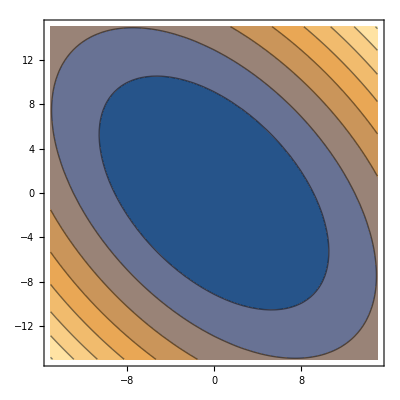

```mathematica
ContourPlot[3x^2+3x y+3 y^2,{x,-15,15},{y,-15,15}]
```

```mathematica
ContourPlot[3x^2+3x y+3 y^2,{x,-15,15},{y,-15,15}]
```

-Graphics-

```mathematica
Clear[a]
```

```mathematica
matrix[a_,b_,c_] ={{1+a^2/c^2,a b/c^2},{a b/c^2,1+b^2/c^2}}
```

{{1+a^2/c^2,(a b)/c^2},{(a b)/c^2,1+b^2/c^2}}

```mathematica
MatrixForm[{{1+a^2/c^2,(a b)/c^2},{(a b)/c^2,1+b^2/c^2}}]
```

(1+a^2/c^2 | (a b)/c^2
(a b)/c^2 | 1+b^2/c^2)

```mathematica
evectors[a_,b_,c_]=Eigenvectors[{{1+a^2/c^2,(a b)/c^2},{(a b)/c^2,1+b^2/c^2}}]
evalues[a_,b_,c_]=Eigenvalues[{{1+a^2/c^2,(a b)/c^2},{(a b)/c^2,1+b^2/c^2}}]
```

{{-b/a,1},{a/b,1}}

{1,(a^2+b^2+c^2)/c^2}

```mathematica
circleparam[radius_,theta_]={radius Cos[theta],radius Sin[theta]}
```

{radius Cos[theta],radius Sin[theta]}

```mathematica
Sqrt[evalues[3,7,2][[2]]]
```

√(31/2)

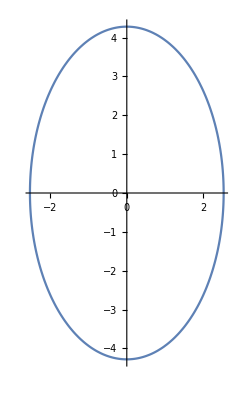

```mathematica
ParametricPlot[{evectors[3,7,2][[1]].circleparam[1,theta],evectors[3,7,2][[2]].circleparam[Sqrt[evalues[3,7,2][[2]]],theta]},{theta,0,2 Pi}]
```

```mathematica
evectors[3,4,2]
```

{{-(-9+√(81+4 ab^2))/(2 ab),1},{-(-9-√(81+4 ab^2))/(2 ab),1}}

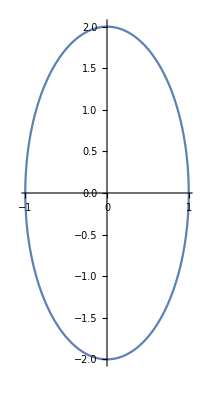

```mathematica
ParametricPlot[{1 Cos[t],2 Sin[t]},{t,0,2 Pi}]
```